```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a0_?NumberQ]:=Block[{p,RRmax,nnGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,tanDelta,fit,nn,δ,L,r,mod,usol,lec},

p=momentum;
RRmax=Rdis;
nnGrid=Npoints;
hDif=RRmax/nnGrid;
L=Lin;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nnGrid,nnGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 Vloc[i hDif,lam,c0,d0,a0]-(L(L+1))/(i hDif)^2),{i,1,nnGrid}]];
Wmat=Table[-hDif^3 mh2 Wnoloc[i hDif,j hDif,p^2/(2 μ),lam,c0,d0,a0],{i,1,nnGrid},{j,1,nnGrid}]; 

bcol=ConstantArray[0,nnGrid];
ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Kmat+Wmat;

(*bcol⟦-1⟧=- hDif p(Cos[p RRmax]+Sin[p RRmax]Tan[p RRmax]);*)
bcol⟦-1⟧=- beta[RRmax,p,L,hDif];
(*Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1-hDif p Tan[p RRmax];*)
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[RRmax,p,L,hDif];

usol=LinearSolve[Amat,bcol];

wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
tanDelta= (RiccatiBesselJ[p RRmax,L]/RiccatiBesselN[p RRmax,L])-(usol⟦-1⟧/RiccatiBesselN[p RRmax,L]);


tanDelta
]
```

```mathematica
Scatt1[cc_?NumberQ,ll_?NumberQ]:=Block[{f,w},
(* 1/2 is to have μ instead of m*)
f=Replace[w,NDSolve[{w'[r]+w[r]^2- mh2 V[r,ll,cc]==0,w[0]==10^20},w,{r,0,R}]⟦1,1⟧];R-f[R]^-1]
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 *)
LEC={(*{0.16,1,-5.23609711,-0.2508527567},{0.2,1,-6.21155090,-0.01411577035},{0.3,1,-9.04089890,0.9058334635},{0.35,1,-10.66481819,1.562725218},{0.4,1,-12.42824554,2.36543082},{0.45,1,-14.33104515,3.3244409},{0.5,1,-16.37322998,4.450396189},{0.55,1,-18.55475197,5.753778748},{0.6,1,-20.87557983,7.245120228},{0.65,1,-23.33569527,8.935015304},{0.7,1,-25.93508911,10.83416803},{0.75,1,-28.67371368,12.95315533},{0.8,1,-31.55156555,15.30282946},{0.85,1,-34.56868362,17.89442822},{0.9,1,-37.72501221,20.7388847},{0.95,1,-41.02048416,23.84721094},*){1,1,-44.45520020,27.23128363},{1.05,1,-48.02915573,30.90286676},{1.1,1,-51.74223328,34.87341855},{1.2,1,-59.58599854,43.76101396},{1.5,1,-86.45745087,78.9169705},{2,1,-142.37614441,172.7038298},{3,1,-295.95935059,559.0134636},{4,1,-505.20166016,1397.569451},{6,1,-1090.66113281,6311.303676},{10,1,-2929.47631836,89436.18522}};
```

```mathematica
nGrid     =250;
R             =10;
ErangeMeV={0.001};(*Range[0.001,2,1];*)
PrangeFM=(Sqrt[2 μ #]/hbar)&/@ErangeMeV;

aff=5.;
hbar=197.327053;
m=938.92;
m1=3 m;m2=m;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;

Lrel=0;

V[r_,lam_,Cc_]:=Cc Exp[-lam r^2];

Vloc[r_,lam_,Cc_,Dd_,Aa_]:=2 Cc (3 Aa/(3 Aa+lam))^(3/2) Exp[-(3 Aa lam/(3 Aa+lam)) r^2]+8 Dd (3 Aa^2/(12 Aa^2+16 Aa lam+lam^2))^(3/2) Exp[-(12 Aa lam (Aa+lam)/(12 Aa^2+16 Aa lam+lam^2)) r^2];

Wnoloc[r_,rp_,e_,lam_,Cc_,Dd_,Aa_]:=-(4 Pi r rp) (

27/8 (3/2 Aa)^(3/2) 1/mh2 Exp[-(15/16) Aa (r^2+rp^2)] ((-(4 (Aa 15/16)^2 r^2+(Aa 15/16)^2 rp^2-2 (Aa 15/16))-mh2 e) SphericalBesselJ[0,I (Aa 18/16) r rp]-4 (Aa 15/16) (Aa 18/16) r rp I/Sqrt[3] SphericalBesselJ[1,I (Aa 18/16) r rp])

-2 27 (3/2 Aa)^(3/2) Cc (Aa/(4 Aa+lam))^(3/2) SphericalBesselJ[0,I (9 Aa (Aa+lam))/(2 (4 Aa+lam)) r rp] Exp[-(3 Aa (5 Aa+8 lam))/(4 (4 Aa+lam)) r^2-(3 Aa (5 Aa+2 lam))/(4 (4 Aa+lam)) rp^2]

-27 (3/2 Aa)^(3/2) Dd (Aa/(4 Aa+5 lam))^(3/2) SphericalBesselJ[0,I (9 (4 Aa^2+8 Aa lam+3 lam^2))/(2 (16 Aa+20 lam)) r rp] Exp[-(3 (20 Aa^2+52 Aa lam+27 lam^2))/(4 (16 Aa+20 lam)) r^2-(3 (20 Aa^2+28 Aa lam+3 lam^2))/(4 (16 Aa+20 lam)) rp^2]
);
```

```mathematica
SetSharedVariable[sl]
sl={};
ParallelDo[

λ=0.25 LEC⟦nn⟧[[1]]^2;
C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];α0=3/2 aff^(-2);

TanDel=Chop[SolveSecular[R,nGrid,#,Lrel,λ,C0,D0,α0]&/@PrangeFM];
DelDeg=180/Pi ArcTan[TanDel];
AppendTo[sl,-TanDel[[#]]/PrangeFM[[#]]^(2 Lrel+1)&/@Range[1,Length[PrangeFM]]];
Print[λ,"  ",α0,"  ",sl[[-1]][[1]]];
,{nn,Range[Length[LEC]]}];
```

General::munfl: Exp[-709.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.724] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.988] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-708.945] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.789] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.637] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

2.25  0.06  7.99302

9.  0.06  8.13543

0.5625  0.06  8.13543

0.25  0.06  8.27076

0.3025  0.06  8.27076

25.  0.06  8.55749

4.  0.06  7.95105

1.  0.06  8.06179

0.36  0.06  8.22365

0.275625  0.06  8.30016

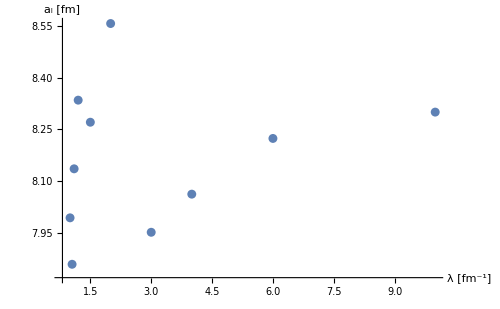

```mathematica
ListPlot[Transpose[{LEC[[All,1]],Flatten[sl]}],AxesLabel->{"λ [fm^-1]","a_l [fm]"},ImageSize->500,PlotRange->Full]
```

```mathematica
Grid[{{ListPlot[Transpose[{ErangeMeV,DelDeg}],PlotRange->Full,AxesLabel->{"k_rel^2/(2 μ) [MeV]","δ_l [Deg]"},PlotLabel->Style["l = "<>ToString[Lrel]<>"     α = "<>ToString[α0]<>" fm^-2",Orange,16],ImageSize->500],ListPlot[Transpose[{PrangeFM hbar,sl}],AxesLabel->{"k_rel [MeV]","a_l [fm]"},ImageSize->500]
}}]
```

```mathematica
Plot3D[W[x,xp,0.0,λ,C0,D0,α0],{x,0,10},{xp,0,10},ImageSize->Large,PlotRange->Full]
```

-Graphics3D-